```mathematica
"For CH"
```

```mathematica
Subscript[β, sfg]=Subscript[Β, sfg] °
Subscript[β, vis]=Subscript[Β, vis] °
Subscript[β, ir]=Subscript[Β, ir] °
Subscript[γ, sfg]=Subscript[Γ, sfg] °
Subscript[γ, vis]=Subscript[Γ, vis] °
Subscript[γ, ir]=Subscript[Γ, ir] °
```

° Β_sfg

° Β_vis

° Β_ir

° Γ_sfg

° Γ_vis

° Γ_ir

```mathematica
"Refractive index"
```

```mathematica
Subscript[n, 1,sfg]=Subscript[n, 1,vis]=Subscript[n, 1,ir]=1
```

1

```mathematica
Subscript[n, 2,sfg]=1.36
Subscript[n, 2,vis]=1.36
Subscript[n, 2,ir]=1.36
```

1.36

1.36

1.36

```mathematica
Subscript[n, m,sfg]=1.16
Subscript[n, m,vis]=1.16
Subscript[n, m,ir]=1.16
```

1.16

1.16

1.16

```mathematica
"Conservation of Momentum"
```

```mathematica
Subscript[Β, ir]=55
```

55

```mathematica
Subscript[Β, vis]=60
Subscript[ω, vis]=18797
Subscript[ω, ir]=2900
```

60

18797

2900

```mathematica
Subscript[ω, sfg]=Subscript[ω, vis]+Subscript[ω, ir]
```

21697

```mathematica
Subscript[Β, sfg]=ArcSin[(Subscript[ω, vis] Sin[Subscript[β, vis]]+Subscript[ω, ir] Sin[Subscript[β, ir]])/Subscript[ω, sfg]]/°
```

ArcSin[((18797 √3)/2+2900 Cos[35 °])/21697]/°

```mathematica
"Snell's Law"
```

```mathematica
Subscript[γ, sfg]=ArcSin[(Sin[Subscript[β, sfg]] Subscript[n, 1,sfg])/Subscript[n, 2,sfg]]
Subscript[γ, vis]=ArcSin[(Sin[Subscript[β, vis]] Subscript[n, 1,vis])/Subscript[n, 2,vis]]
Subscript[γ, ir]=ArcSin[(Sin[Subscript[β, ir]] Subscript[n, 1,ir])/Subscript[n, 2,ir]]
```

0.684359

0.690319

0.646401

```mathematica
"Fresnel Factors"
```

```mathematica
Subscript[L, xx,sfg]= (Subscript[n, 1,sfg] 2 Cos[Subscript[γ, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[γ, sfg]] + Subscript[n, 2,sfg] Cos[Subscript[β, sfg]])Cos[Subscript[β, sfg]]
Subscript[L, xx,vis]= (Subscript[n, 1,vis] 2 Cos[Subscript[γ, vis]])/(Subscript[n, 1,vis] Cos[Subscript[γ, vis]] + Subscript[n, 2,vis] Cos[Subscript[β, vis]])Cos[Subscript[β, vis]]
Subscript[L, xx,ir]= (Subscript[n, 1,ir] 2 Cos[Subscript[γ, ir]])/(Subscript[n, 1,ir] Cos[Subscript[γ, ir]] + Subscript[n, 2,ir] Cos[Subscript[β, ir]])Cos[Subscript[β, ir]]

Subscript[L, yy,sfg]= (Subscript[n, 1,sfg] 2 Cos[Subscript[β, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[β, sfg]] +Subscript[n, 2,sfg] Cos[Subscript[γ, sfg]])
Subscript[L, yy,vis]= (Subscript[n, 1,vis] 2 Cos[Subscript[β, vis]])/(Subscript[n, 1,vis] Cos[Subscript[β, vis]] +Subscript[n, 2,vis] Cos[Subscript[γ, vis]])
Subscript[L, yy,ir]= (Subscript[n, 1,ir] 2 Cos[Subscript[β, ir]])/(Subscript[n, 1,ir] Cos[Subscript[β, ir]] +Subscript[n, 2,ir] Cos[Subscript[γ, ir]])

Subscript[L, zz,sfg]=  (Subscript[n, 2,sfg] 2 Cos[Subscript[β, sfg]])/(Subscript[n, 1,sfg] Cos[Subscript[γ, sfg]] +Subscript[n, 2,sfg] Cos[Subscript[β, sfg]])(Subscript[n, 1,sfg]/Subscript[n, m,sfg])^2 Sin[Subscript[β, sfg]]
Subscript[L, zz,vis]=  (Subscript[n, 2,vis] 2 Cos[Subscript[β, vis]])/(Subscript[n, 1,vis] Cos[Subscript[γ, vis]] +Subscript[n, 2,vis] Cos[Subscript[β, vis]])(Subscript[n, 1,vis]/Subscript[n, m,vis])^2 Sin[Subscript[β, vis]]
Subscript[L, zz,ir]= (Subscript[n, 2,ir] 2 Cos[Subscript[β, ir]])/(Subscript[n, 1,ir] Cos[Subscript[γ, ir]] +Subscript[n, 2,ir] Cos[Subscript[β, ir]])(Subscript[n, 1,ir]/Subscript[n, m,ir])^2 Sin[Subscript[β, ir]]
```

0.538598

0.531371

0.580188

0.652875

0.645737

0.691387

0.604035

0.603217

0.601746

```mathematica
"R(r for C∞v)=(β_(a, a, c))/(β_(c, c, c))"
```

```mathematica
R=0.27
```

0.27

```mathematica
Subscript[β, c,c,c]=1
Subscript[Ν, s]=1
```

1

1

```mathematica
"For SSP"
```

```mathematica
SSP=Subscript[L, yy,sfg] Subscript[L, yy,vis] Subscript[L, zz,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c]((1+R)Cos[θ]-(1-R)Cos[θ]^3)
```

0.126844 (1.27 Cos[θ]-0.73 Cos[θ]^3)

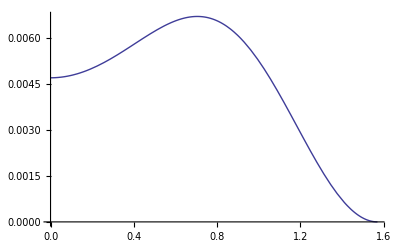

```mathematica
Plot[SSP^2,{θ,0Degree, 90 Degree}]
```

```mathematica
"For SPS"
```

```mathematica
SPS=Subscript[L, yy,sfg] Subscript[L, zz,vis] Subscript[L, yy,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3)
```

0.0993842 (Cos[θ]-Cos[θ]^3)

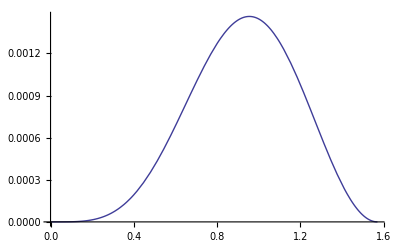

```mathematica
Plot[SPS^2,{θ,0Degree, 90 Degree}]
```

```mathematica
"For PSS"
```

```mathematica
PSS=Subscript[L, zz,sfg] Subscript[L, yy,vis] Subscript[L, yy,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3)
```

0.098431 (Cos[θ]-Cos[θ]^3)

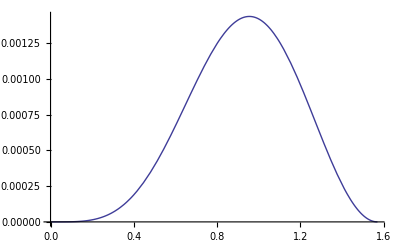

```mathematica
Plot[PSS^2,{θ,0Degree, 90 Degree}]
```

```mathematica
"For PPP"
```

```mathematica
PPP=-Subscript[L, xx,sfg] Subscript[L, xx,vis] Subscript[L, zz,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c]((1+R)Cos[θ]-(1-R)Cos[θ]^3)-Subscript[L, xx,sfg] Subscript[L, zz,vis] Subscript[L, xx,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3)+Subscript[L, zz,sfg] Subscript[L, xx,vis] Subscript[L, xx,ir] 1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3)+Subscript[L, zz,sfg] Subscript[L, zz,vis] Subscript[L, zz,ir] Subscript[Ν, s] Subscript[β, c,c,c](R Cos[θ]+(1-R)Cos[θ]^3)
```

-0.000831083 (Cos[θ]-Cos[θ]^3)-0.0861087 (1.27 Cos[θ]-0.73 Cos[θ]^3)+0.219255 (0.27 Cos[θ]+0.73 Cos[θ]^3)

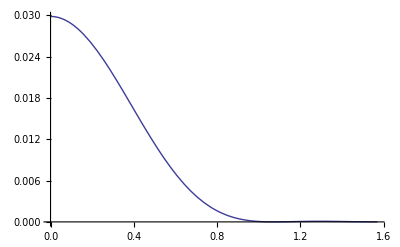

```mathematica
Plot[PPP^2,{θ,0Degree, 90 Degree}]
```

```mathematica
"For CH-Symmetric Stretching"
```

```mathematica
θ=th °
```

° th

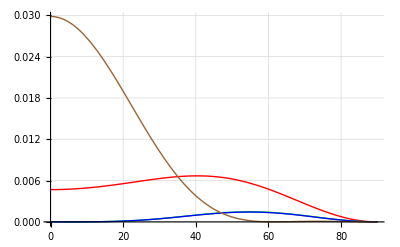

```mathematica
Plot[{SSP^2,SPS^2,PSS^2,PPP^2},{th,0,90},PlotStyle->{Red,Green, Blue,Brown},PlotRange->All,GridLines->Automatic]
```